```mathematica
kk[zmax_,NN_]:=zmax^NN/(NN!)
```

```mathematica
kk[0.5,20]
```

3.9199×10^-25

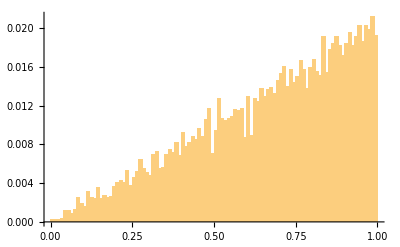

```mathematica
g1=Table[q=RandomReal[];√q,{n,1,10000}];
Histogram[g1,{0.01},"Probability"]
```

```mathematica
NQ=100000;
tb=Table[NN=20;
c=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{n,1,NN}]];
c[[1]],{q,1,NQ}];
```

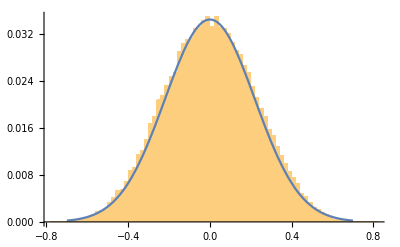

```mathematica
σ=0.22;Show[Histogram[tb,{0.02},"Probability"],Plot[0.152/(20σ) Exp[-x^2/(2 σ^2)],{x,-0.7,0.7},PlotRange->All]]
```

```mathematica
NQ=100000;
tb=Table[NN=20;
c=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{n,1,NN}]];
g1=Table[1,{n,1,NN}];
c.g1,{q,1,NQ}];
```

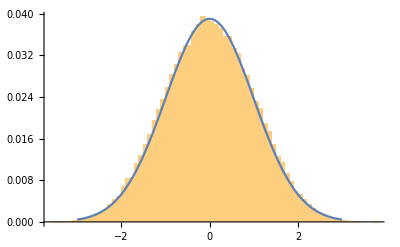

```mathematica
σ=1;Show[Histogram[tb,{0.1},"Probability"],Plot[0.78/(20σ) Exp[-x^2/(2 σ^2)],{x,-3,3}]]
```

```mathematica
Series[Erf[x],{x,0,2}]
```

(2 x)/(√π)+O[x]^3

```mathematica
P1=Erf[z/(x √20)]/.{z->0.1,x->0.01}
Log[10^-20]/Log[P1]
```

0.998435

29395.4

```mathematica
fft1=FindFit[his,A PDF[NormalDistribution[0,B],x],{A,B},x]
```

{A→487.011,B→0.296342}

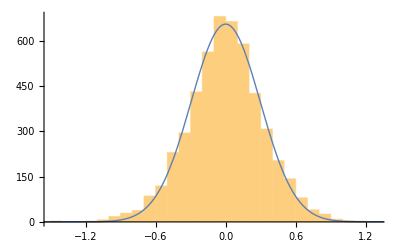

```mathematica
Show[Histogram[tb,{0.1}],Plot[A PDF[NormalDistribution[0,B],x] /.fft1,{x,-2,2},PlotRange->All, PlotStyle->Thick]]
```

```mathematica
σ1[b_,x_]:= 1.0/(1.0+E^(-2b x))
σ2[b_,x_]:=1/2(1+(b x)/(√(1+(b x)^2)))
σ3[b_,x_]:=If[x>1/b,1,If[x<-1/b,0,(b x+1)/2]]
σ4[b_,x_]:=If[x>π/(2b),1,If[x<-π/(2b),0,(1+Sin[b x])/2]]
```

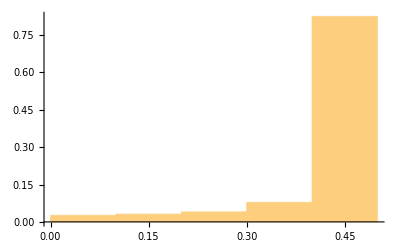

```mathematica
Histogram[Abs[0.5-σ2[10,tb[[1]]]],5,"Probability"]
```

```mathematica
cnt[dx_,w_]:=Module[{s,tsg,NNx},s=0;NNx=Length[tb[[1]]];For[n=1,n<=NNx,n++,If[Abs[σ1[w,tb[[1,n]]]-0.5]<dx,s++]];
N[s/NNx]]
```

```mathematica
atb=Table[{Print[α];α,btb=Table[{b,1/cnt[α,b]},{b,1,10,1}];1/u/.FindFit[btb,u x,u,x][[1]]},{α,0.02,0.3,0.02}];
```

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

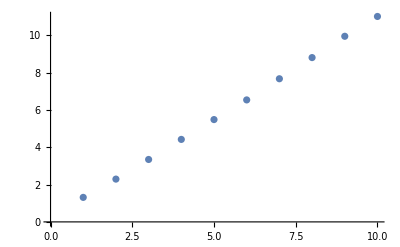

```mathematica
ListPlot[btb]
```

```mathematica
fv=u x+v x^2;
fft3 = FindFit[atb,fv, {u,v}, x]
```

{u→2.41936,v→1.93588}

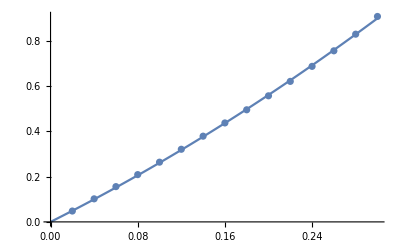

```mathematica
Show[ListPlot[atb],Plot[fv/.fft3,{x,0,0.3}]]
```

```mathematica
P = fv/b/.fft3
```

(2.41936 x+1.93588 x^2)/b

```mathematica
P/.{x->0.1,b->2}
```

0.130648

```mathematica
cnt[0.1,2]
```

0.13318

```mathematica
cnt[0.1,2]^5 10^5
cnt[0.05,2]^10
```

4.18982

1.67105×10^-12

```mathematica
cnt[0.2,1]
cnt[0.2,1]^10 10^3
cnt[0.2,1]^20
```

0.52284

1.52647

2.33011×10^-6